# Práctica 3

## EJERCICIO 1

-Graphics-

```mathematica
Clear["Global`*"]
```

```mathematica
a=Table[i,{i,1,11,2}];b=Table[i,{i,0,7}];c=Table[i,{i,6,11}];
```

```mathematica
u=Union[a,b,c]
```

{0,1,2,3,4,5,6,7,8,9,10,11}

```mathematica
i=Intersection[a,b,c]
```

{7}

## CONJUNTOS

```mathematica
Intersection[Complement[a,b],Complement[a,c],Complement[a,b]]
```

{}

```mathematica
Union[Complement[a,b],Complement[a,c]]
```

{1,3,5,9,11}

```mathematica
Complement[a,Intersection[b,c]]
```

{1,3,5,9,11}

#### Conjunto Potencia

```mathematica
Length[a]
```

6

```mathematica
pot=Subsets[a]
```

{{},{1},{3},{5},{7},{9},{11},{1,3},{1,5},{1,7},{1,9},{1,11},{3,5},{3,7},{3,9},{3,11},{5,7},{5,9},{5,11},{7,9},{7,11},{9,11},{1,3,5},{1,3,7},{1,3,9},{1,3,11},{1,5,7},{1,5,9},{1,5,11},{1,7,9},{1,7,11},{1,9,11},{3,5,7},{3,5,9},{3,5,11},{3,7,9},{3,7,11},{3,9,11},{5,7,9},{5,7,11},{5,9,11},{7,9,11},{1,3,5,7},{1,3,5,9},{1,3,5,11},{1,3,7,9},{1,3,7,11},{1,3,9,11},{1,5,7,9},{1,5,7,11},{1,5,9,11},{1,7,9,11},{3,5,7,9},{3,5,7,11},{3,5,9,11},{3,7,9,11},{5,7,9,11},{1,3,5,7,9},{1,3,5,7,11},{1,3,5,9,11},{1,3,7,9,11},{1,5,7,9,11},{3,5,7,9,11},{1,3,5,7,9,11}}

```mathematica
Length[pot]
```

64

## EJERCICIO 2

-Graphics-

```mathematica
Clear["Global`*"]
```

```mathematica
GCD[539000,338800]
```

15400

```mathematica
LCM[539000,338800]
```

11858000

## DIVISIBILIDAD

### MCM y MCD

```mathematica
LCM[18,12]
```

36

```mathematica
GCD[18,12]
```

6

```mathematica
LCM[18,12]*GCD[18,12]==18*12
```

True

### PRIMOS

```mathematica
PrimeQ[101]
```

True

```mathematica
Table[Prime[i],{i,1,100}]
```

{2,3,5,7,11,13,17,19,23,29,31,37,41,43,47,53,59,61,67,71,73,79,83,89,97,101,103,107,109,113,127,131,137,139,149,151,157,163,167,173,179,181,191,193,197,199,211,223,227,229,233,239,241,251,257,263,269,271,277,281,283,293,307,311,313,317,331,337,347,349,353,359,367,373,379,383,389,397,401,409,419,421,431,433,439,443,449,457,461,463,467,479,487,491,499,503,509,521,523,541}

```mathematica
CoprimeQ[25,9](*PRIMOS ENTRE SI*)
```

True

```mathematica
NextPrime[7]
```

11

```mathematica
FactorInteger[18]
```

{{2,1},{3,2}}

```mathematica
Divisors[18]
```

{1,2,3,6,9,18}

## EJECICIO 3

-Graphics-

```mathematica
Clear["Global`*"]
```

```mathematica
Solve[Binomial[x,3]==Binomial[x,2]]
```

{{x→0},{x→1},{x→5}}

## EJERCICIO 4

-Graphics-

```mathematica
Clear["Global`*"]
```

```mathematica
f[x_]=x^3+1;g[x_]=2x+5;
```

```mathematica
f[g[x]]
```

1+(5+2 x)^3

```mathematica
g[f[x]]
```

5+2 (1+x^3)

## EJERCICIO 5

-Graphics-

```mathematica
Clear["Global`*"]
```

```mathematica
f[x_]=x/a;g[x_]=c*x+d;
```

```mathematica
Reduce[f[g[x]]==g[f[x]],x]
```

(d==0&&a≠0)||a==1

d==0 y a!=0 y c=cualquier valor real
a==1 y c y d= cualquier valor real

## EJECICIO 6

-Graphics-

```mathematica
Clear["Global`*"]
```

```mathematica
f[x_]=Piecewise[{{4227x/101+47/125,x<=0},{2x+3,x>0}}]
```

Piecewise[{{47/125+(4227 x)/101, x≤0}, {3+2 x, x>0}, {0, True}}]

```mathematica
f[1/2]
```

4

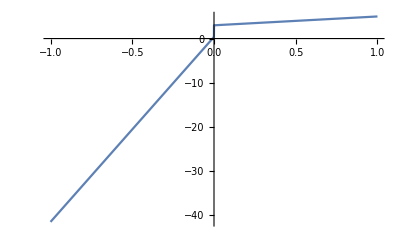

```mathematica
Plot[f[x],{x,-1,1}]
```

## FUNCIONES A TROZOS

```mathematica
Clear["Global`*"]
```

### PARCIAL I 2023

```mathematica
f[x_]=Piecewise[{{-x-2,x<=-2},{x^2-4,-2<x<0},{-x^3-4,x>=0}}]
```

Piecewise[{{-2-x, x≤-2}, {-4+x^2, -2<x<0}, {-4-x^3, x≥0}, {0, True}}]

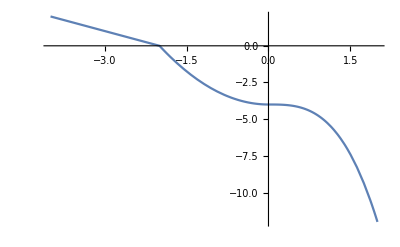

```mathematica
Plot[f[x],{x,-4,2},ColorFunction->Red]
```

```mathematica
g[x_]=Piecewise[{{-2^x,x<=0},{-Cos[x],0<x<Pi/2},{x-Pi/2,x>=Pi/2}}]
```

Piecewise[{{-2^x, x≤0}, {-Cos[x], 0<x<π/2}, {-π/2+x, x≥π/2}, {0, True}}]

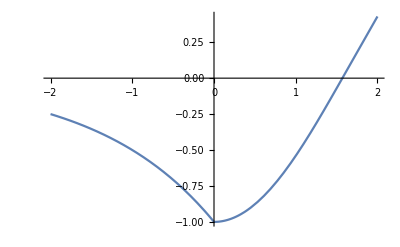

```mathematica
Plot[g[x],{x,-2,2}]
```

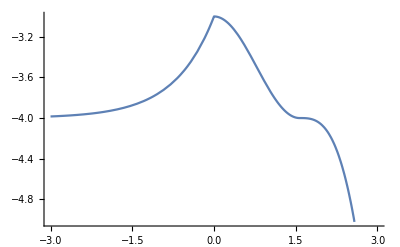

```mathematica
Plot[g[f[x]],{x,-3,3}]
```

## EJECICIO 7

-Graphics-

```mathematica
Clear["Global`*"]
```

```mathematica
FactorInteger[112233]
```

{{3,1},{11,1},{19,1},{179,1}}

```mathematica
FactorInteger[332211]
```

{{3,1},{11,1},{10067,1}}

## EJERCICIO 8

-Graphics-

```mathematica
Clear["Global`*"]
```

```mathematica
f[x_]=6x-2
```

-2+6 x

```mathematica
Solve[f[x1]==f[x2],{x1,x2}]
```

{{x2→x1}}

## RESOLVER ECUACIONES

```mathematica
Solve[6x-2==0,x]
```

{{x→1/3}}

```mathematica
Solve[{x+y==5,x-y==3},{x,y}]
```

{{x→4,y→1}}

```mathematica
Reduce[{x+a*y==5,x-a*y==3},{x,y}]
```

x==4&&a≠0&&y==1/a

## EJECICIO 9

-Graphics-

```mathematica
Clear["Global`*"]
```

```mathematica
Binomial[120,6]
```

3652745460

## COMBINATORIA

```mathematica
Clear["Global`*"]
```

```mathematica
(*Variaciones son Combinaciones de m n x Permutaciones de n*)
```

```mathematica
Reduce[{Binomial[m,n+2]*(n+2)! ==20*Binomial[m,n]*n!,Binomial[n,2]*2! ==110,m>=n},{m,n}]
```

Reduce::fexp: Warning: Reduce used FunctionExpand to transform the system. Since FunctionExpand transformation rules are only generically correct, the solution set might have been altered.

m==16&&n==11

## EJERCICIO 10

-Graphics-

```mathematica
Clear["Global`*"]
```

```mathematica
e=Table[2i-1,{i,1,100}]
```

{1,3,5,7,9,11,13,15,17,19,21,23,25,27,29,31,33,35,37,39,41,43,45,47,49,51,53,55,57,59,61,63,65,67,69,71,73,75,77,79,81,83,85,87,89,91,93,95,97,99,101,103,105,107,109,111,113,115,117,119,121,123,125,127,129,131,133,135,137,139,141,143,145,147,149,151,153,155,157,159,161,163,165,167,169,171,173,175,177,179,181,183,185,187,189,191,193,195,197,199}

```mathematica
a=Intersection[e,Table[3*(2*i-1),{i,1,100}]]
```

{3,9,15,21,27,33,39,45,51,57,63,69,75,81,87,93,99,105,111,117,123,129,135,141,147,153,159,165,171,177,183,189,195}

```mathematica
b=Intersection[e,Table[2i-1,{i,81,100}]]
```

{161,163,165,167,169,171,173,175,177,179,181,183,185,187,189,191,193,195,197,199}

```mathematica
Intersection[a,b]
```

{165,171,177,183,189,195}

```mathematica
Union[a,b]
```

{3,9,15,21,27,33,39,45,51,57,63,69,75,81,87,93,99,105,111,117,123,129,135,141,147,153,159,161,163,165,167,169,171,173,175,177,179,181,183,185,187,189,191,193,195,197,199}

```mathematica
Length[a]
```

33

```mathematica
Length[b]
```

20

```mathematica
Complement[e,a] (*A'*)
```

{1,5,7,11,13,17,19,23,25,29,31,35,37,41,43,47,49,53,55,59,61,65,67,71,73,77,79,83,85,89,91,95,97,101,103,107,109,113,115,119,121,125,127,131,133,137,139,143,145,149,151,155,157,161,163,167,169,173,175,179,181,185,187,191,193,197,199}

```mathematica
Complement[e,b](*B'*)
```

{1,3,5,7,9,11,13,15,17,19,21,23,25,27,29,31,33,35,37,39,41,43,45,47,49,51,53,55,57,59,61,63,65,67,69,71,73,75,77,79,81,83,85,87,89,91,93,95,97,99,101,103,105,107,109,111,113,115,117,119,121,123,125,127,129,131,133,135,137,139,141,143,145,147,149,151,153,155,157,159}